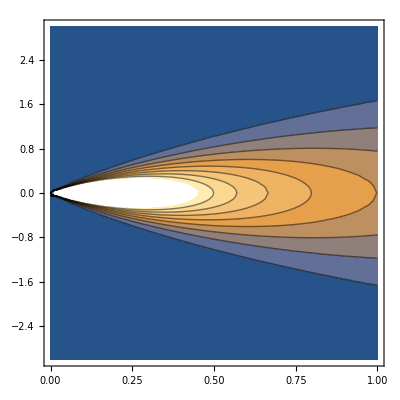

```mathematica
ContourPlot[{PDF[NormalDistribution[0,t],x]},{t,0,1},{x,-3,3}]
```

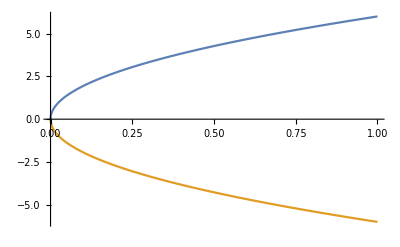

```mathematica
Plot[{6*t^0.49,-6*t^0.49},{t,0,1}]
```

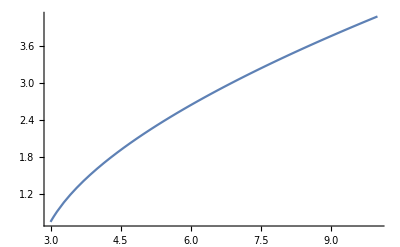

```mathematica
Plot[√(2t  Log[Log[t]]),{t,3,10}]
```

```mathematica
√(2t  Log[Log[t]])/.t-> 1//N
```

ⅈ ∞

Modulus of continuity

```mathematica
Plot[{6.31 √t,6 t^0.49,2.5 √(t  Log[1/t]),3.3 √(2t  Log[Log[1/t]])},{t,0,0.01},PlotRange->Full]
```

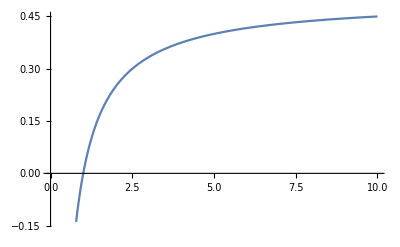

```mathematica
Plot[(x-1)/(2x),{x,0,10}]
```

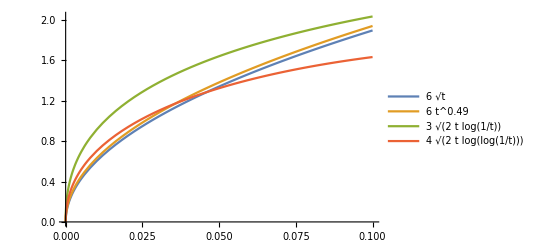

```mathematica
Plot[{6 √t,6 t^0.49,3 √(2t  Log[1/t]),4 √(2t  Log[Log[1/t]])},{t,0,0.1},PlotRange->Full,PlotLegends->"Expressions"]
```

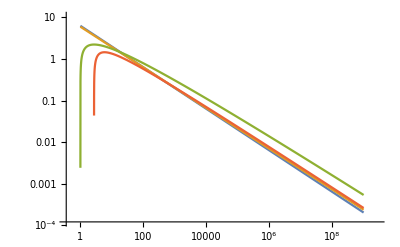

```mathematica
LogLogPlot[{6.31 √(1/s),6 (1/s)^0.49,2.6 √(2/s Log[s]),3.3 √(2/s  Log[Log[s]])},{s,1,10^9}]
```

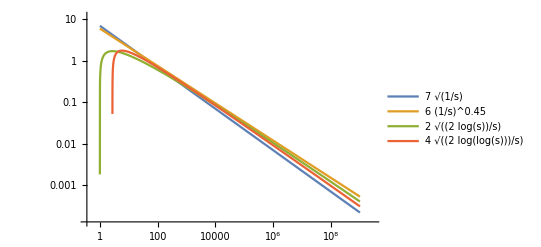

```mathematica
LogLogPlot[{7 √(1/s), 6(1/s)^0.45,2 √(2/s Log[s]),4 √(2/s  Log[Log[s]])},{s,1,10^9},PlotLegends->"Expressions"]
```

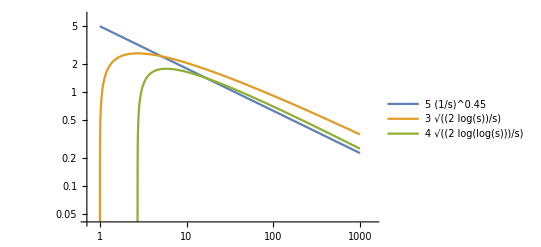

```mathematica
LogLogPlot[{ 5(1/s)^0.45,3 √(2/s Log[s]),4 √(2/s  Log[Log[s]])},{s,1,10^3},PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Plot3D[If[d0 d1 < 0.5/(√n),1-Exp[-2 n  *d0* d1],1],{d0,0,2},{d1,0,2} ,PlotRange->Full],{n,1,10}]
```